## MICA: Measurement, Instrumentation, Control and Analysis

## Hammerstein System Identification: Quadratic

#### Ariel Mobius, MIT 7 May 2026

#### Revisions

2025		Dec	04	Updated from previous versions
			08	Changed to using SVD based Toeplitz impulse response function estimates
			09	Added more keywords

#### Keywords

Hammerstein System, Wiener System, NL System, LN System, Static Nonlinearity, Quadratic Nonlinearity, Linear Dynamic Subsystem, Impulse Response Function, Transfer Function, Second-Order System, Low-Pass Filter, Under-Damped System, Natural Frequency, Damping Ratio, Static Gain, Inverse Laplace Transform, Sampling Interval, Gaussian White Noise, Stochastic Input, Numerical Convolution, ListConvolve, Probability Density Function, Probability Distribution Function,  Auto-Correlation Function, Cross-Correlation Function, Biased Correlation, Covariance Function, Toeplitz Matrix, Singular Value Decomposition (SVD), Pseudo-Inverse, Regularization, Singular Value Thresholding, Bussgang’s Theorem, Scaling Ambiguity, Variance Accounted For (VAF), Residuals, Prediction Error, Deconvolution, Wiener Deconvolution, ListDeconvolve, Internal Signal Estimation, Cross-Plotting, Polynomial Fitting, LinearModelFit, Iterative Refinement, Non-Parametric Estimation, Parametric Model, Levenberg-Marquardt Algorithm, NonlinearModelFit, Objective Function, Model Complexity, FindFormula, Model Discovery, System Identification, Black Box Modeling, Input-Output Analysis

#### Objectives

The purpose of this MICA Module is to define Hammerstein systems and introduce techniques which under certain circumstances enables Hammerstein systems to be characterized experimentally.

#### Hammerstein systems

A static nonlinearity (e.g., cuber, hard limiter, etc) followed by a linear dynamic subsystem is called a Hammerstein system after the German mathematician Adolf Hammerstein (if you can read German see https://de.wikipedia.org/wiki/Adolf_Hammerstein) who studied such systems.

-Graphics-

Here we see a Hammerstein system consisting of a static nonlinear element, n(·), followed by a linear dynamic subsystem as represented by an impulse response function, h(τ). The input to the Hammerstein system is denoted by, x(t), and the output from the Hammerstein system is denoted by, y(t). An internal signal u(t) is the output from the  static nonlinear element, n(·), and is also the input to the linear dynamic component, h(τ).
Sometimes Hammerstein systems are called NL systems because there is a static nonlinearity (N) followed by a linear dynamic system (L). An LN system consists of a  linear dynamic element (L) followed by a nonlinear static element (N) and is called a Wiener system. Wiener system identification is the subject of another MICA Notebook.

-Graphics-

In this MICA Notebook we will simulate a Hammerstein system and attempt to discover,  n(·) and h(τ), purely from the input, x(t), and output, y(t), data sets.

#### Note

You can progress through this Notebook by clicking on the   ■   at the start of each region of code.  This will execute  (evaluate) the region of code associated with   ■   and any results of the code execution will be generated and added to the Notebook. After inspecting the results and reading subsequent text you can use the mouse scroll wheel (if available) to scroll down to the next    ■     .

The whole Notebook can be executed by selecting Evaluation from the menu above and clicking on Evaluate Notebook. While it is OK to do this here, it can be potentially disastrous if this is done in MICA Notebooks containing code to run experiments.

#### Create Hammerstein system

As an example lets start by making the nonlinear static element, n(·), a saturation nonlinearity and generate a second-order, low-pass, under-damped impulse response function, h(τ), (to model the linear dynamic element).

#### Saturation static nonlinearity

In this example we will make the static nonlinearity a quadratic:

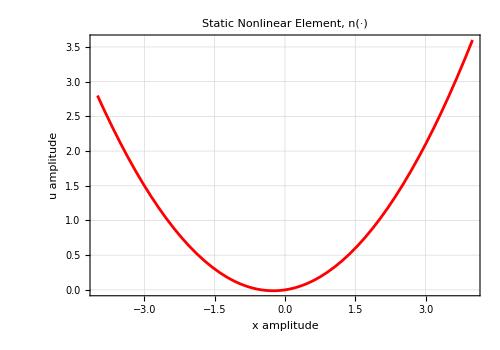

```mathematica
"■"; n[xx_]:=0.2 xx^2+0.1xx;
Plot[n[xx],{xx,-4,4},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},FrameLabel->{"x amplitude","u amplitude"},AspectRatio->0.7,PlotLabel->"Static Nonlinear Element, n(·)",PlotRange->All,ImageSize->500]
```

#### Generate h(τ)

Lets choose a second-order low-pass  subsystem. The general  transfer function  for such a  sub system is :

```mathematica
"■"; H[s_,α_,ω_,ζ_]:=(α ω^2)/(s^2+2 ζ ω s+ω^2)(* *)
```

If we inverse Laplace transform this transfer function then we get:

```mathematica
"■"; InverseLaplaceTransform[H[s,α,ω,ζ],s,τ]//FullSimplify
```

(ⅇ^(-ζ τ ω) α ω Sinh[√(-1+ζ^2) τ ω])/(√(-1+ζ^2))

This is the system continuous (or symbolic) unit impulse response function which we will denote h in order to distinguish it from the sampled version (see below) which we will denote, h. We also denote the continuous lag domain by τ to distinguish it from the sampled version  (see below) which is denoted by τi.

```mathematica
"■"; h[τ_,α_,ω_,ζ_]:=(ⅇ^(-ζ τ ω) α ω Sinh[√(-1+ζ^2) τ ω])/(√(-1+ζ^2))
```

Lets make the static gain, α = 1, the  natural frequency, ω = 60  rad/s  (around 10 Hz) , and the damping parameter  ζ = 0.7  .

```mathematica
"■"; h[τ_]:=h[τ,1,60,0.7]//FullSimplify//Re
```

Lets plot this:

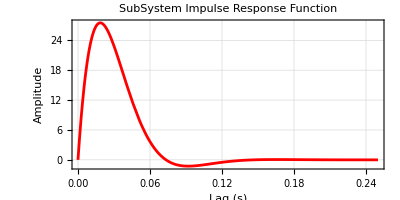

```mathematica
"■"; Plot[h[τ],{τ,0,0.25},GridLines->Automatic,PlotStyle->Red,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"SubSystem Impulse Response Function",PlotRange->All,ImageSize->Automatic->600]
```

Notice that this impulse response function “dies out” by around 0.15 s.

We will need to sample this symbolic version of the impulse response function to produce a sampled version. To do this we need to specify the inter-sample interval, Δτ, and the maximum lag, τMax. Lets make the sampling increment be 2 ms (i.e., a sampling rate of 500 Hz) and the maximum lag be 0.25 s (as above).

```mathematica
"■"; Δτ=0.002; τMax=0.25;
```

We can now generate a sampled version of the lag domain, τ:

```mathematica
"■"; τi=Range[0,τMax, Δτ];
```

and a sampled version of the impulse response function:

```mathematica
"■"; hi=h[τi];
```

Now we can plot both the continuous and sampled versions of h:

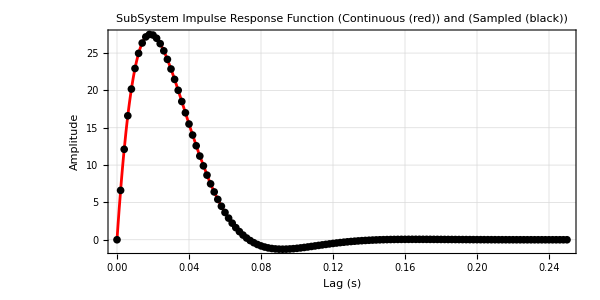

```mathematica
"■"; Show[
Plot[h[τ],{τ,0,0.25},PlotStyle->Red,Frame->True,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"SubSystem Impulse Response Function (Continuous (red)) and (Sampled (black))",PlotRange->All,ImageSize->600],
ListPlot[{τi,hi}ᵀ,PlotStyle->Black]]
```

It is always a good idea to plot the individual points in the impulse response function to check that the sampling rate is high enough given the time course of the function. It is best to have plenty of points (e.g., > 5) covering the initial rise of the impulse response function. It is also best to have a domain (whose last value is τMax) which is 1.5 × to 2 × the time it takes for the impulse response to “die out”. If these conditions are not met then resample the original continuous (symbolic) impulse response function with a more appropriate sampling interval, Δτ, and maximum lag, τMax.

Note that the area under the impulse response function should equal the static gain, which is 1.0 in this case. Lets check by crude rectangular numeric integration:

```mathematica
"■";Total[hi] Δτ
```

0.998832

This is close enough.

#### Generate the input, x(t), the unobservable internal signal, u(t) and the output, y(t)

#### Generate Gaussian white noise signal, x(t)

We start by generating 20 seconds of a Gaussian white noise input, x(t), sampled at around 500 Hz, with a mean of 0 and a standard deviation of 1. Note that we could have used pretty much any stochastic input here except a stochastic binary input (which is not sufficient to identify a nonlinear system). Note that as before we generate a sampled version of the time domain and specify a maximum time, tMax. Note also that we use the same sampling interval in time, Δt, as we used for lag, Δτ.

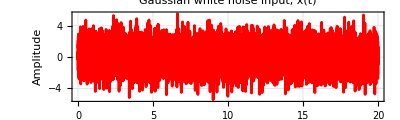

```mathematica
"■"; tMax=20.0;
Δt=Δτ;
ti=Range[0.0,tMax, Δt];
x=Table[RandomVariate[NormalDistribution[0,1.5]],Length[ti]]; 
ListLinePlot[{ti,x}ᵀ,PlotTheme->"Detailed",PlotRange->All, PlotStyle->Red,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Gaussian white noise input, x(t)",ImageSize->Automatic->800]
```

#### Pass the input, x(t), through the static nonlinear element, n(·), to generate the internal signal, u(t)

We now pass x(t) through our static nonlinearity, n(·), to produce the internal signal, u(t):

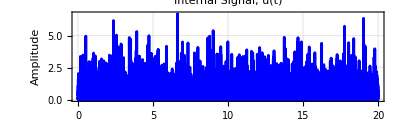

```mathematica
"■";u=n[x];
ListLinePlot[{ti,u}ᵀ,PlotTheme->"Detailed",PlotRange->All, PlotStyle->Blue,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Internal Signal, u(t)",ImageSize->Automatic->800]
```

#### Convolve, h(τ), with u(t) to produce, the output, y(t)

We now numerically convolve our sampled input, x(t), with the sampled version of our impulse response function, h(τ), to generate the internal signal, u(t):

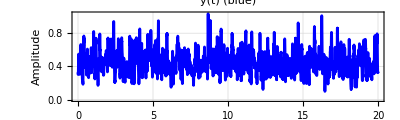

```mathematica
"■";y=Δt ListConvolve[hi,u,{1,1}] ;
ListLinePlot[{ti,y}ᵀ,PlotTheme->"Detailed",PlotRange->All, PlotStyle->Blue,Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"y(t) (blue)",ImageSize->Automatic->800]
```

#### Compare input and output probability density functions

We now calculate the input and output probability density functions using Mathematica’s SmoothHistogram[ ] function which determines the probability density functions via a different technique than the usual Histogram[ ] function. There is a whole area of statistics devoted to different probability density function determination methods.
Notice that while the original input, x(t) is Gaussian:

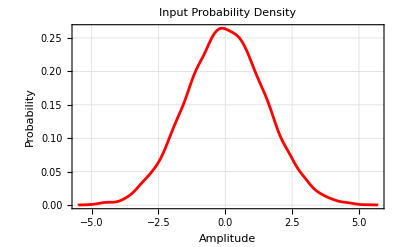

```mathematica
"■"; SmoothHistogram[x,Automatic,"PDF",PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Amplitude","Probability"},LabelStyle->{12,Black},PlotStyle->Red,PlotLabel->"Input Probability Density",ImageSize->Automatic->400]
```

The output, y(t), is a little “less”  Gaussian:

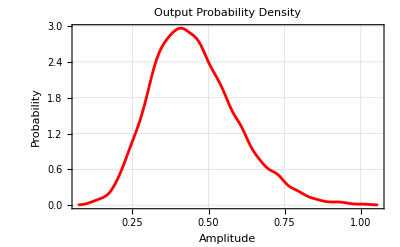

```mathematica
"■"; SmoothHistogram[y,Automatic,"PDF",PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Amplitude","Probability"},LabelStyle->{12,Black},PlotStyle->Red,PlotLabel->"Output Probability Density",ImageSize->Automatic->400]
```

A linear system perturbed by a Gaussian stochastic input (does not need to be white) will produce a Gaussian stochastic output. If the output from a system driven by a Gaussian stochastic input is non Gaussian then this is clear evidence that the system is nonlinear. The output probability density function looks Gaussian so we cannot at this point conclude that we have a nonlinear system. Remember to distinguish a necessary condition from a sufficient condition: if the input is Gaussian and the output is Gaussian it could still be a nonlinear system.

#### Compare input and output probability distribution functions

Lets calculate the smoothed input and output probability distribution functions:

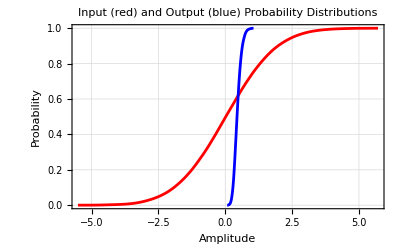

```mathematica
"■"; Show[
SmoothHistogram[x,Automatic,"CDF",PlotStyle->Red,PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Amplitude","Probability"},LabelStyle->{12,Black},PlotLabel->"Input (red) and Output (blue) Probability Distributions",ImageSize->Automatic->400],
SmoothHistogram[y,Automatic,"CDF",PlotStyle->Blue]]
```

#### Hammerstein system identification

We now ask if it is possible to determine the two internal subsystems, namely, h(τ) and n(·) solely from the input, x(t), and output, y(t), signals.
Lets see what happens when we compute the nonparametric impulse response function, hi1(τ), between the input, x(t), and the output, y(t).

To do this we compute the input auto-correlation function, xacf(τ), and the cross-correlation function between x(t) and y(t), xyccf(τ).

Define a function to perform biased auto- and cross-correlation functions (strictly speaking it calculates auto- and cross-covariance functions)

```mathematica
"■"; cor[x_,y_,m_]:= With[{n=Length[x],xMn=Mean[x],yMn=Mean[y]},Table[((x[[1;;n-j]]-xMn).(y[[1+j;;n]]-yMn)) /n,{j,0,m}] ]
```

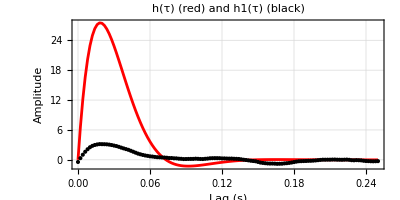

```mathematica
"■"; xacf=cor[x,x,τMax/Δt];
xyccf=cor[x,y,τMax/Δt];

(*toe=ToeplitzMatrix[xacf];
invtoe=Inverse[toe];
hi1=(invtoe.xyccf)/Δt;*)

{U,S,V}=SingularValueDecomposition[ToeplitzMatrix[xacf]];
threshold=0.1 Max[S]; (*Keep only significant singular values*)
Sinv=DiagonalMatrix[1/Max[#,threshold]&/@Diagonal[S]];
hi1=1/Δt V.Sinv.Transpose[U].xyccf;

ListPlot[{{τi,hi}ᵀ,{τi,hi1}ᵀ},Joined->{True,False},PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"h(τ) (red) and h1(τ) (black)",PlotRange->All,ImageSize->Automatic->600]
```

If we multiply h(τ) by α and divide n(·) by α there will be no change in the output, y(t). In other words there is a scaling constant, α , that can freely move from h(τ) to n(·).

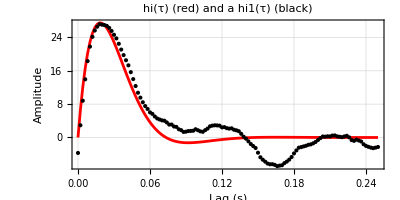

```mathematica
"■"; ListPlot[{{τi,hi}ᵀ,{τi,hi1/(Δτ Total[hi1])}ᵀ},Joined->{True,False},PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"hi(τ) (red) and a hi1(τ) (black)",PlotRange->All,ImageSize->Automatic->600]
```

This is a remarkable result!! It shows that despite the presence of a major static nonlinearity such as a cuber, the stochastic system identification techniques were able to nevertheless get an estimate of the Hammerstein system’s dynamic linear element. This amazing result (for the case of cross-correlation) seems to have been first discovered by Julian Bussgang (https://en.wikipedia.org/wiki/Julian_J._Bussgang) in 1951 during his Master’s thesis research when he was a student at the Research Lab for Electronics (RLE) at MIT (https://en.wikipedia.org/wiki/Bussgang_theorem).

#### Predict output, y1(t)

We can check to see how much of the output variance we can predict simply using our estimate of the impulse response function:

```mathematica
"■";y1=Δt ListConvolve[hi1,x,{1,1}] ;
```

Compute the residuals

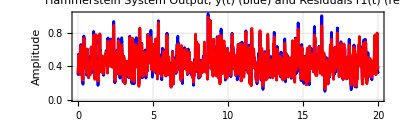

```mathematica
"■"; r1=y-y1;
ListLinePlot[{{ti,y}ᵀ,{ti,r1}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Hammerstein System Output, y(t) (blue) and Residuals r1(t) (red)",ImageSize->Automatic->800]
```

```mathematica
"■"; vaf1=100.0 (1-Variance[r1]/Variance[y])
```

7.48187

This VAF is low. The remaining variance not accounted for by our linear dynamic model is a mixture of noise and or nonlinearities.  At this point we could assume that the system is linear and proceed to find a suitable parametric model. Alternatively we could decide that it is worth exploring the possibility that the system is nonlinear. We might assume that the system is a Wiener system and proceed to carry out Wiener system ID or we could assume that it might be a Hammerstein system and proceed as follows:

#### Predict u(t)

Now that we have hi1(τ), if we could find its dynamic inverse, hi1Inv(τ), then we could convolve hi1Inv(τ) with the output, y(t), to produce a prediction, u1(t), of the internal signal, u(t). Stated another way, we would like to deconvolve the impulse response function from the output, y(t), to yield an estimate of u(t).

#### Deconvolution of hi1(τ) from the output, y(t), to predict the internal signal, u(t)

Mathematica contains some powerful deconvolution methods. They are usually used to reduce blur in images but they work for signals also:

```mathematica
"■"; u1a=1/Δτ ListDeconvolve[hi1,y,Method->"Wiener"];
```

ListDeconvolve[ ] produces u1a(t) shifted by half the length of hi1 plus 1. So we need to trim this first part off and add to the end:

```mathematica
"■"; nn=Length[x]; m=Length[hi1];
u1=Join[u1a[[1+(m/2);;nn]],u1a[[1;;m/2]]];
```

#### Predict n(·)

Now that we have an estimate for u1(t) we can predict the form of the static nonlinearity by simply cross-plotting x vs u1 :

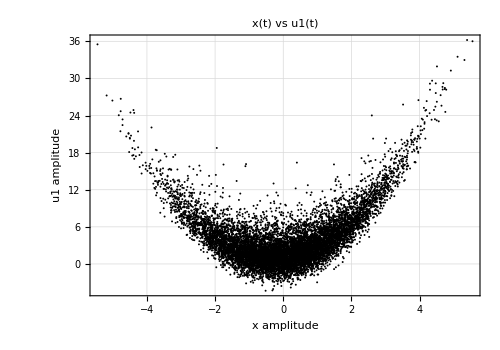

```mathematica
"■"; ListPlot[{x,u1}ᵀ,PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"x amplitude","u1 amplitude"},AspectRatio->0.7,PlotLabel->"x(t) vs u1(t)",PlotRange->All,ImageSize->500]
```

This looks like a classic saturation nonlinearity. So lets estimate the four parameters of a saturation nonlinearity model using our trusty Levenberg-Marquardt nonlinear minimization technique to fit to the x(t) vs u1(t) cross-plot after we give some initial estimates for our 4 parameters by inspection of the plot above:

We can find an approximation to the estimate, n1(·), of n(·) above by fitting a high-order polynomial to the x(t) vs u1(t) cross-plot:

```mathematica
"■"; n1=LinearModelFit[{x,u1}ᵀ, {1,xx,xx^2,xx^3,xx^4,xx^5,xx^6,xx^7,xx^8,xx^9},xx]["Function"];
```

Lets plot this estimate, n1(·), of the nonlinearity together with the cross-plot of x(t) vs u1(t):

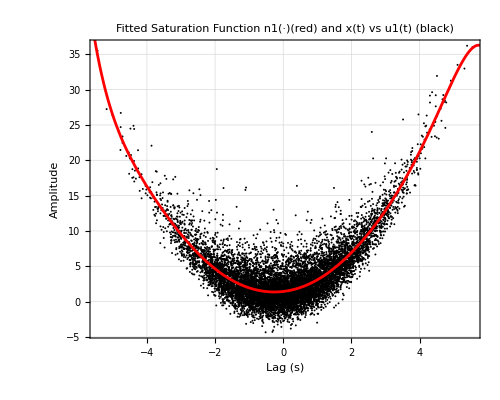

```mathematica
"■";Show[
ListPlot[{x,u1}ᵀ,PlotStyle->Black,PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Lag (s)","Amplitude"},PlotLabel->"Fitted Saturation Function n1(·)(red) and x(t) vs u1(t) (black)", PerformanceGoal->"Quality",ImageSize->500,AspectRatio->0.8,PerformanceGoal->"Quality"],
Plot[n1[xx],{xx,-6,6},PlotRange->All,PlotStyle->Red]]
```

The spread in the points about the fitted model (red) is large but lets carry on in any case.

#### Re-predict internal signal, u2(t)

Now that we have the estimate, n1(·), we can transform the input, x(t), through it to re-predict the internal signal, u2(t):

```mathematica
"■"; u2=n1[x];
```

#### Re-estimate the impulse response function

Now that we have a new prediction of the internal signal, u2(t), we can re-estimate the impulse response function but now between u2(t) and y(t):

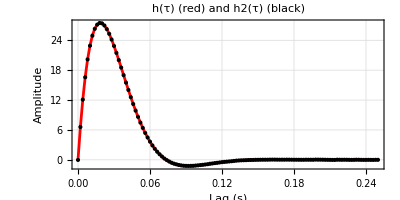

```mathematica
"■"; uacf=cor[u2,u2,τMax/Δt];
uyccf=cor[u2,y,τMax/Δt];

(*toe=ToeplitzMatrix[uacf];
invtoe=Inverse[toe];
hi2=(invtoe.uyccf)/Δt;*)

{U,S,V}=SingularValueDecomposition[ToeplitzMatrix[uacf]];
threshold=0.1 Max[S]; (*Keep only significant singular values*)
Sinv=DiagonalMatrix[1/Max[#,threshold]&/@Diagonal[S]];
hi2=1/Δt V.Sinv.Transpose[U].uyccf;

ListPlot[{{τi,hi}ᵀ,{τi,hi2/(Δτ Total[hi2])}ᵀ},Joined->{True,False},PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"h(τ) (red) and h2(τ) (black)",PlotRange->All,ImageSize->Automatic->600]
```

And we can now generate a new output prediction:

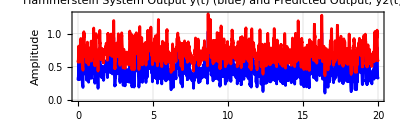

```mathematica
"■";y2=Δt ListConvolve[hi2,u2,{1,1}] ;
ListLinePlot[{{ti,y}ᵀ,{ti,y2}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Hammerstein System Output y(t) (blue) and Predicted Output, y2(t) (red)",ImageSize->Automatic->800]
```

The prediction looks ok, so lets calculate the residuals, r2(t):

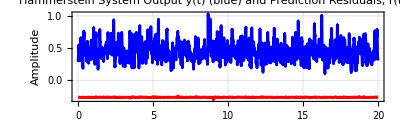

```mathematica
"■"; r2=y-y2;
ListLinePlot[{{ti,y}ᵀ,{ti,r2}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Hammerstein System Output y(t) (blue) and Prediction Residuals, r(t) (red)",ImageSize->Automatic->800]
```

```mathematica
"■"; vaf2=100.0 (1-Variance[r2]/Variance[y])
```

99.9648

This is dramatically higher than our earlier VAF, so we are making very good progress:

```mathematica
"■"; vaf1
```

7.48187

However if we can assume that the noise levels are really low we might be able to do even better than this. We will therefor attempt to refine our estimates of h(τ) and n(·) to see if we can achieve an even higher VAF.

#### Redo the deconvolution of hi2() from y(t) to yield a new estimate of u(t)

```mathematica
"■"; u3a=1/Δτ ListDeconvolve[hi2/(Δτ Total[hi2]),y,Method->"Wiener"];
```

The Method used in ListDeconvolve[ ] is based on a method developed by Norbert Wiener. But this method has nothing to do with the use of Wieners name in association with LN systems.

Remember that ListDeconvolve[ ] produces u3a(t) shifted by half the length of hi2 plus 1. So we need to trim this first part off and add to the end:

```mathematica
"■"; u3=Join[u3a[[1+(m/2);;nn]],u3a[[1;;m/2]]];
```

#### Re-predict n(·)

Now that we have a new estimate, u3(t), we can predict the form of the static nonlinearity by simply cross-plotting x vs u3 :

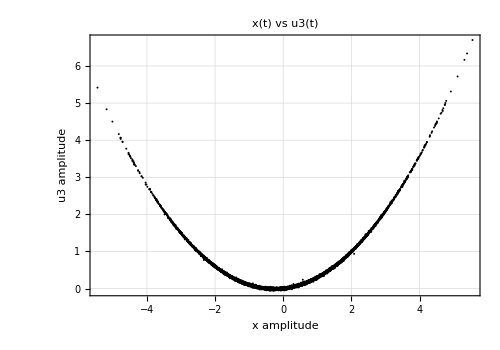

```mathematica
"■"; ListPlot[{x,u3}ᵀ,PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"x amplitude","u3 amplitude"},AspectRatio->0.7,PlotLabel->"x(t) vs u3(t)",PlotRange->All,ImageSize->500]
```

Now we have much less spread in the points.

So lets re-estimate the four parameters of a saturation nonlinearity model using Levenberg - Marquardt nonlinear minimization technique to fit to the x (t) vs u3 (t) cross - plot  above to give a new estimate n2(·) :

```mathematica
"■";  n2=LinearModelFit[{x,u3}ᵀ, {1,xx,xx^2,xx^3,xx^4,xx^5,xx^6,xx^7,xx^8,xx^9},xx]["Function"];
```

Lets plot this estimate, n2(·), of the nonlinearity together with the cross-plot of x(t) vs u3(t):

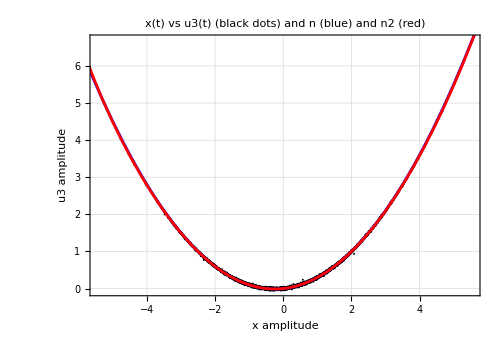

```mathematica
"■"; Show[
ListPlot[{x,u3}ᵀ,PlotTheme->"Detailed",PlotStyle->Black,Frame->True,LabelStyle->{12,Black},FrameLabel->{"x amplitude","u3 amplitude"},AspectRatio->0.7,PlotLabel->"x(t) vs u3(t) (black dots) and n (blue) and n2 (red)",PlotRange->All,ImageSize->500],
Plot[{n[xx],n2[xx]},{xx,-7,7},PlotStyle->{Blue,Red}]]
```

The fitted function is similar to the actual Hammerstein system nonlinearity.

#### Re-predict internal signal, u4(t)

Now that we have the estimate, n2(·), we can transform the input, x(t), through it to re-predict the internal signal, u4(t):

```mathematica
"■"; u4=n2[x];
```

#### Re-estimate the impulse response function

Now that we have a new prediction of the internal signal, u4(t), we can re-estimate the impulse response function but now between u4(t) and y(t):

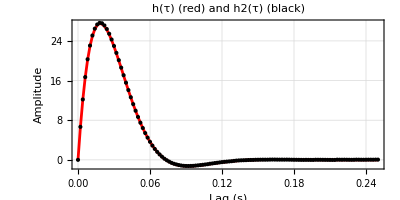

```mathematica
"■"; uacf=cor[u4,u4,τMax/Δt];
uyccf=cor[u4,y,τMax/Δt];

(*toe=ToeplitzMatrix[uacf];
invtoe=Inverse[toe];
hi3=(invtoe.uyccf)/Δt;*)

{U,S,V}=SingularValueDecomposition[ToeplitzMatrix[uacf]];
threshold=0.1 Max[S]; (*Keep only significant singular values*)
Sinv=DiagonalMatrix[1/Max[#,threshold]&/@Diagonal[S]];
hi3=1/Δt V.Sinv.Transpose[U].uyccf;

ListPlot[{{τi,hi}ᵀ,{τi,hi3}ᵀ},Joined->{True,False},PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Lag (s)","Amplitude"},AspectRatio->0.5,PlotLabel->"h(τ) (red) and h2(τ) (black)",PlotRange->All,ImageSize->Automatic->600]
```

And we can now generate a new output prediction:

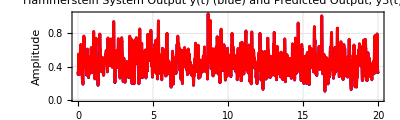

```mathematica
"■";y3=Δt ListConvolve[hi3,u4,{1,1}] ;
ListLinePlot[{{ti,y}ᵀ,{ti,y3}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Hammerstein System Output y(t) (blue) and Predicted Output, y3(t) (red)",ImageSize->Automatic->800]
```

The prediction is so good it is difficult to see the difference between y(t) and y3(t). So lets calculate the residuals, r3(t):

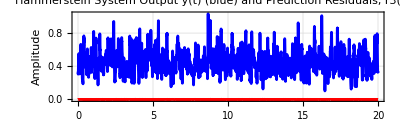

```mathematica
"■"; r3=y-y3;
ListLinePlot[{{ti,y}ᵀ,{ti,r3}ᵀ},PlotTheme->"Detailed",PlotRange->All, PlotStyle->{Blue,Red},Frame->True,LabelStyle->{12,Black},FrameLabel->{"Time (s)","Amplitude"},AspectRatio->0.3,PlotLabel->"Hammerstein System Output y(t) (blue) and Prediction Residuals, r3(t) (red)",ImageSize->Automatic->800]
```

```mathematica
"■"; vaf3=100.0 (1-Variance[r3]/Variance[y])
```

99.9991

This is a tad higher than our previous VAF, but we have basically accounted for all the output variance.

```mathematica
"■"; {vaf1,vaf2,vaf3}
```

{7.48187,99.9648,99.9991}

#### Re-predict n(·)

Now that we have a new estimate, u4(t), we can predict the form of the static nonlinearity by simply cross-plotting x vs u4 :

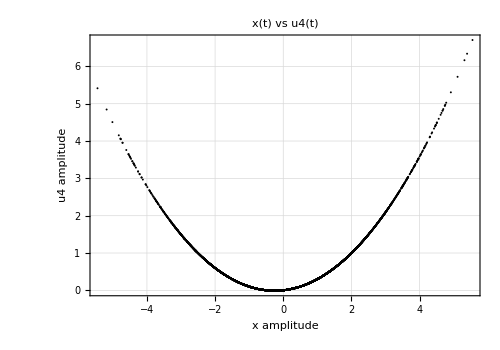

```mathematica
"■"; ListPlot[{x,u4}ᵀ,PlotTheme->"Detailed",PlotStyle->{Red,Black},Frame->True,LabelStyle->{12,Black},FrameLabel->{"x amplitude","u4 amplitude"},AspectRatio->0.7,PlotLabel->"x(t) vs u4(t)",PlotRange->All,ImageSize->500]
```

Now we have a really low spread in the points.

So lets re-estimate the four parameters of a saturation nonlinearity model using Levenberg - Marquardt nonlinear minimization technique to fit to the x (t) vs u4 (t) cross - plot  above to give a new estimate n3(·) :

```mathematica
"■";  n3=LinearModelFit[{x,u4}ᵀ, {1,xx,xx^2,xx^3,xx^4,xx^5,xx^6,xx^7,xx^8,xx^9},xx]["Function"];
```

Lets plot this estimate, n3(·), of the nonlinearity together with the cross-plot of x(t) vs u3(t):

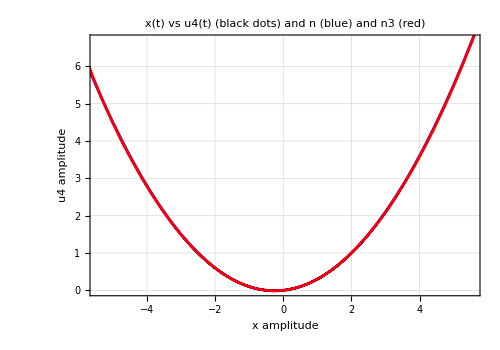

```mathematica
"■"; Show[
ListPlot[{x,u4}ᵀ,PlotTheme->"Detailed",PlotStyle->Black,Frame->True,LabelStyle->{12,Black},FrameLabel->{"x amplitude","u4 amplitude"},AspectRatio->0.7,PlotLabel->"x(t) vs u4(t) (black dots) and n (blue) and n3 (red)",PlotRange->All,ImageSize->500],
Plot[{n[xx],n3[xx]},{xx,-7,7},PlotStyle->{Blue,Red}]]
```

#### Parametric models

Now that we have a good nonparametric model for the impulse response function it is appropriate to go one more step and generate a parametric (equation based) model for it.

#### Parametric impulse response function model

By observation of the shape of hi2(τ) it looks as though it might be well approximated (fitted) by a second-order low-pass underdamped impulse response function.

```mathematica
"■"; h[τ_,α_,ω_,ζ_]:=(ⅇ^(-ζ τ ω) α ω Sinh[√(-1+ζ^2) τ ω])/(√(-1+ζ^2))
```

We start by defining an objective function to be minimized. Lets find the 3 parameters of the parametric second order low-pass underdamped impulse response function which minimize the sum of squared differences between it and the best nonparametric impulse response function model we determined, namely, h2(τ).

```mathematica
"■";rmsError[α_,ω_,ζ_]:=With[{n=Length[hi2]},Abs[Sqrt[((hi2-h[τi,α,ω,ζ]).(hi2-h[τi,α,ω,ζ]))/(n-2)]]]
```

From inspection of h2(τ) above lets estimate that the natural frequency will be near 7 Hz. Which in rad/s is  :

```mathematica
"■";ωω=2π 7.0;
```

The system is clearly only slightly underdamped (i.e., a little less than 1.0) so lets set it to be:

```mathematica
"■";ζζ=0.8;
```

The static gain (i.e., overall gain) is the area under the impulse response function which we forced to be 1, so lets set it to be:

```mathematica
"■";αα=1.0
```

1.

```mathematica
"■";rmsError[αα,ωω,ζζ] (* rms error before nonlinear least squares fit *)
```

5.87871

Now lets plot the parametric impulse response function with these estimates together with the nonparametric impulse response function, h3(τ):

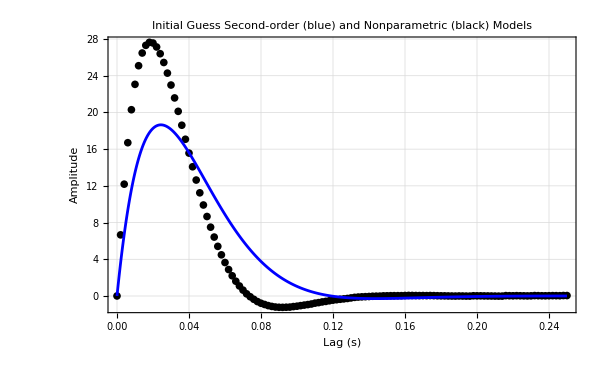

```mathematica
"■";Show[
ListPlot[{τi,hi3}ᵀ,PlotRange->All,Frame->True,PlotStyle->Black,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Lag (s)","Amplitude"},PlotLabel->"Initial Guess Second-order (blue) and Nonparametric (black) Models", PerformanceGoal->"Quality",ImageSize->600],
Plot[h[τ,αα,ωω,ζζ],{τ,0,τMax},PlotStyle->Blue,PlotRange->All,PlotPoints->1000,PerformanceGoal->"Quality"]]
```

Our initial estimates are clearly off. Lets estimate the four parameters using our trusty Levenberg-Marquardt nonlinear minimization technique:

```mathematica
"■";nlm=NonlinearModelFit[{τi,hi3}ᵀ,h[τ,α,ω,ζ],{{α,αα},{ω,ωω},{ζ,ζζ}},τ, Method->"LevenbergMarquardt"];
nlm["BestFitParameters"]
{αα,ωω,ζζ}={α,ω,ζ}/.nlm["BestFitParameters"];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{α→1.00565,ω→60.0697,ζ→0.701767}

```mathematica
"■";rmsError[αα,ωω,ζζ](* rms error after nonlinear least squares fit *)
```

7.63565

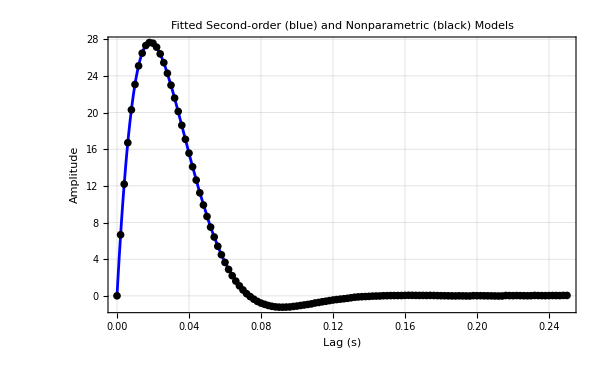

```mathematica
"■";Show[
Plot[h[τ,αα,ωω,ζζ],{τ,0,τMax},PlotRange->All,Frame->True,PlotStyle->Blue,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Lag (s)","Amplitude"},PlotLabel->"Fitted Second-order (blue) and Nonparametric (black) Models", PerformanceGoal->"Quality",ImageSize->600],
ListPlot[{τi,hi3}ᵀ,PlotStyle->Black,PlotRange->All,PerformanceGoal->"Quality"]]
```

Nice! Clearly we have an excellent fit and there is no point going to a higher order model.

The original “true” values for the static gain, natural frequency and damping were:

```mathematica
{1,60,0.7}
```

{1,60,0.7}

The estimated values are

```mathematica
"■";{αα,ωω,ζζ}
```

{1.00565,60.0697,0.701767}

These are almost exactly the same. So we have identified the parametric dynamic linear component of the Hammerstein system.

#### Parametric static nonlinear element model

It remains for us to find a parametric model for the static nonlinearity. The last estimate of the static nonlinearity was n3. Mathematica provides a function called FindFormula[ ] which attempts to discover static models which fit a data set. It takes a while because it is trying a huge number of candidate models:

```mathematica
"■"; fit=FindFormula[{x,u4}ᵀ,uu,10,All ]
```

This discovery function returns suitable static models together with a “Score” and a measure of “Complexity”. A “good” model is one which has a high Score (a good fit) but a low level of complexity under the assumption that simplicity is important. Using these two criteria we choose the p1 uu + p2 uu^2 model. This model form is exactly the static nonlinearity used in the Hammerstein model. Furthermore  the two parameters of this model are p1 = 0.1 and p2 = 0.1 are has a value near to 10 which is the same as that used when the Wiener system was specified. In other words we have identified the static nonlinearity.

FindFormula does a quick fit and test of a wide range of functions. Lets redo the fit:

```mathematica
"■"; LinearModelFit[{x,u4}ᵀ, {1 xx,xx^2},xx]
```

FittedModel[…]

This model is almost exactly the same static nonlinearity as used in our simulation u = 0.1 x + 0.2 x^2 .

In conclusion we have managed to identify both the static nonlinear part and the linear dynamic part of the the Hammerstein system. 
The Hammerstein system has been identified!!